# Math 223: Homework 10

Ali Heydari

April. 21st, 2021

## Problem 1

Use boundary-layer theory to find a uniform approximation with error of order ϵ^2 for the problem:

				

, 	

Notice that there is no boundary layer in leading order, but one does appear in next order. Compare your solution with the exact solution to this problem.

To find the boundary layer, we can take a look at the coefficient of the first order derivative, i.e. , which is greater than 0. This means that our boundary layer will be at the left boundary, so now solving for the outer layer:



Now substituting this back into the original perturbed ODE, we get that:

 and 

from which we find that  and using the fact that . We can show this with Mathematica:

```mathematica
DSolve[{Subscript[y, 0]'[x]+Subscript[y, 0][x]==0,Subscript[y, 0][0]==E},Subscript[y, 0][x],x]
```

{{y_0[x]→ⅇ^(1-x)}}

So our solution for up to order ϵ is :



We can now continue to find the order ϵ^2 approximation, meaning :

```mathematica
DSolve[{Subscript[y, 1]'[x]+Subscript[y, 1][x]==Exp[1-x],Subscript[y, 1][1]==0},Subscript[y, 1][x],x]
```

{{y_1[x]→ⅇ^(1-x) (-1+x)}}

So putting the first two order solutions together, we get:



So we have successfully found the outer solution. Now to find the inner solution, we introduce a stretch coordinate . So now we want to make sure that the second derivate stays, so we can explicitly find:



now the term δ^-1 is more dominant than the other terms, so we choose that which means that X = x/ϵ.

So we find that the stretch coordinate must be , which yields :



assuming the same solution type as outer solution (i.e. ), we find the first order solution to be:


Now we can do the substitution that , so now we can solve:

```mathematica
DSolve[{Subscript[u, 0]'[X]+Subscript[u, 0][X]==0},Subscript[u, 0][X],X]
```

{{u_0[X]→ⅇ^-X C[1]}}

finding that 

Now using the boundary condition , we can obtain the first order inner solution to be: 




to obtain the next order solution, we can follow the same procedure and get:

```mathematica
DSolve[{Subscript[u, 0]'[X]+Subscript[u, 0][X]== C[1](1-Exp[-X]) + E},Subscript[u, 0][X],X]
```

{{u_0[X]→ⅇ^-X (ⅇ^(1+X)+ⅇ^X C[1]-X C[1])+ⅇ^-X C[2]}}

so the inner solution now becomes:

To determine the constants for the inner solution, we will do the asymptotic matching:

 → 

meaning that  and , so now the inner solution becomes: 



Finally, to find the uniform solution:





and after doing the calculations, we arrive at:

 + 

Now to compare with the exact solution:

```mathematica
NumericalSolution =NDSolve[{0.01 y''[x]+ y'[x]+y[x]==0,y[0]==E,y[1]==1},y[x],{x,0,1}]
```

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
AsymptoticApproximation[x_,ϵ_] = Exp[1-x]*(1 + ϵ*(1-x-Exp[-1/ϵ]))
```

ⅇ^(1-x) (1+(1-ⅇ^(-1/ϵ)-x) ϵ)

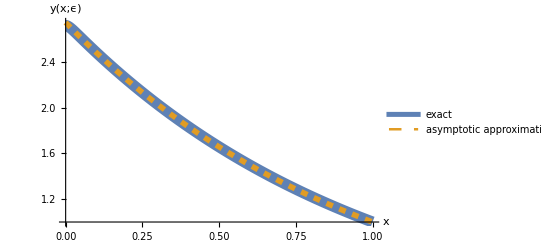

```mathematica
Plot[{y[x]/.NumericalSolution,AsymptoticApproximation[x,0.01]},{x,0,1},PlotLegends->{"exact","asymptotic approximation"},PlotRange->All,PlotStyle->{ Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["y(x;ϵ)", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

## Problem 2

Use boundary-layer methods to find an approximate solution to the initial-value problem

					

,

Show that the leading-order uniform approximation satisfies , but not  for arbitrary  Compare the leading-order uniform approximation with the exact solution to the problem when  and  are constants.

## Problem 3

The function  satisfies:

		

and is subject to boundary conditions   and  . Find two terms in the outer approximation, applying only the boundary condition at . Next, find two terms in the inner approximation for the boundary layer near , which can be assumed to have width , and only applying the boundary condition at . Finally determine the constants of integration in the inner approximation by matching.